```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
a[x_,y_]:={Thickness[0.003],Arrowheads[0.055],Arrow[{{x,-y/2},{x,y/2}}]};
d[x_,y_,r_,color_]:={EdgeForm[{Thickness[0.005],Black}],Lighter[color],Disk[{x,y},r]};
rc[x_,y_,r_,color_]:={EdgeForm[{Black}],Lighter[color],Rectangle[{x-hw,y-hw},{x+hw,y+hw}](*Disk[{x,y},r]*)};
e[x_,y_,dx_,dy_]:={eraserColor,Rectangle[{x-dx/2,y-dy/2},{x+dx/2,y+dy/2}]};
```

```mathematica
holeFillingColor=White;(*Darker[Blend[{Blue,Darker[Cyan]},0.5]];*)
magnonFillingColor=Gray;(*Darker[Red];*)
eraserColor=White;
h=2;
hw=0.2;
r=0.25;
```

-Graphics-

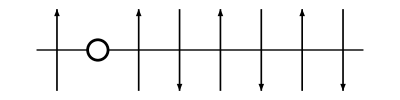

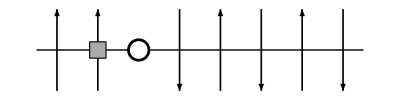

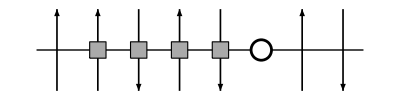

-Graphics-

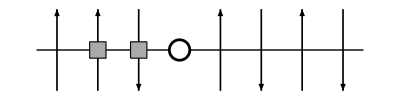

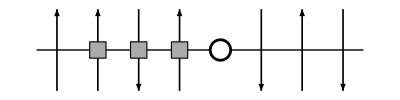

```mathematica
g0=Graphics[(
eraser=Table[e[n,0,1,1],{n,1,8}];
Join[eraser]
)]
g1=Graphics[(
arrows1=Table[a[n,-h*(-1)^n],{n,1,1}];
arrows2=Table[a[n,-h*(-1)^n],{n,3,8}];
(*arrows3=Table[a[n,h*(-1)^n],{n,8,10}];*)
hole=Table[d[n,0,r,holeFillingColor],{n,{2}}];
sites=Table[d[n,0,0.05,Black],{n,1,8}];
baseline={Line[{{0.5,0},{8.5,0}}]};
(*eraser={e[7,0,1,1]};*)
(*dots=Table[d[6.5+n/4,0,0.025,Black],{n,1,3}];*)
insets={
fontSize=24;
Inset[Style["i",fontSize,Black,FontFamily->"Bookman Old Style"],{4,-1.6}],
Inset[Style["i + n",fontSize,Black,FontFamily->"Bookman Old Style"],{8,-1.6}]
};
Join[baseline,(*sites,*)arrows1,arrows2,(*arrows3,*)hole(*,eraser,dots,insets*)]
)]
g2=Graphics[(
arrows1=Table[a[n,-h*(-1)^n],{n,1,1}];
arrows2=Table[a[n,h*(-1)^n],{n,2,2}];
arrows3=Table[a[n,-h*(-1)^n],{n,4,8}];
magnons=Table[rc[n,0,r,magnonFillingColor],{n,2,2}];
hole=Table[d[n,0,r,holeFillingColor],{n,{3}}];
sites=Table[d[n,0,0.05,Black],{n,1,8}];
baseline={Line[{{0.5,0},{8.5,0}}]};
(*spinonLine={Red,Line[{{1.0,0},{2.0,0}}]};*)
(*eraser={e[6,0,1,2.25]};
dots=Table[d[5.5+n/4,0,0.025,Black],{n,1,3}];
insets={
fontSize=24;
Inset[Style["i",fontSize,Black,FontFamily->"Bookman Old Style"],{4,-1.6}],
Inset[Style["i + n",fontSize,Black,FontFamily->"Bookman Old Style"],{8,-1.6}]
};*)
Join[baseline,(*sites,*)arrows1,arrows2,arrows3,magnons,hole(*,eraser,dots,insets*)]
)]
g3=Graphics[(
arrows1=Table[a[n,-h*(-1)^n],{n,1,1}];
arrows2=Table[a[n,h*(-1)^n],{n,2,5}];
arrows3=Table[a[n,-h*(-1)^n],{n,7,8}];
magnons=Table[rc[n,0,r,magnonFillingColor],{n,2,5}];
hole=Table[d[n,0,r,holeFillingColor],{n,{6}}];
sites=Table[d[n,0,0.05,Black],{n,1,8}];
baseline={Line[{{0.5,0},{8.5,0}}]};
(*eraser={e[6,0,1,2.25]};
dots=Table[d[5.5+n/4,0,0.025,Black],{n,1,3}];
insets={
fontSize=24;
Inset[Style["i",fontSize,Black,FontFamily->"Bookman Old Style"],{4,-1.6}],
Inset[Style["i + n",fontSize,Black,FontFamily->"Bookman Old Style"],{8,-1.6}]
};*)
Join[baseline,(*sites,*)arrows1,arrows2,arrows3,magnons,hole(*,eraser,dots,insets*)]
)]
g4=Graphics[(
eraser=Table[e[n,0,1,2],{n,1,10}];
hole={d[2.5,2,r,holeFillingColor]};
magnon={d[6,2,r,magnonFillingColor]};
inset={
(*Inset[Style[" hole",24,Black,FontFamily->"Bookman Old Style"],{3.5,1.5}],
Inset[Style[" magnon",24,Black,FontFamily->"Bookman Old Style"],{7.5,1.5}],*)
(*Inset[Style["1/(N - 1)(⟨∑)_(i  = 1)^Na_i^†a_i⟩ = 1/2",18,Black,FontFamily->"Bookman Old Style"],{5.5,0}]*)
};
Join[eraser,(*,hole,magnon,*)inset]
)]
g5=Graphics[(
arrows1=Table[a[n,-h*(-1)^n],{n,1,1}];
arrows2=Table[a[n,h*(-1)^n],{n,2,3}];
arrows3=Table[a[n,-h*(-1)^n],{n,5,8}];
magnons=Table[rc[n,0,r,magnonFillingColor],{n,2,3}];
hole=Table[d[n,0,r,holeFillingColor],{n,{4}}];
sites=Table[d[n,0,0.05,Black],{n,1,8}];
baseline={Line[{{0.5,0},{8.5,0}}]};
(*eraser={e[6,0,1,2.25]};
dots=Table[d[5.5+n/4,0,0.025,Black],{n,1,3}];
insets={
fontSize=24;
Inset[Style["i",fontSize,Black,FontFamily->"Bookman Old Style"],{4,-1.6}],
Inset[Style["i + n",fontSize,Black,FontFamily->"Bookman Old Style"],{8,-1.6}]
};*)
Join[baseline,(*sites,*)arrows1,arrows2,arrows3,magnons,hole(*,eraser,dots,insets*)]
)]
g6=Graphics[(
arrows1=Table[a[n,-h*(-1)^n],{n,1,1}];
arrows2=Table[a[n,h*(-1)^n],{n,2,4}];
arrows3=Table[a[n,-h*(-1)^n],{n,6,8}];
magnons=Table[rc[n,0,r,magnonFillingColor],{n,2,4}];
hole=Table[d[n,0,r,holeFillingColor],{n,{5}}];
sites=Table[d[n,0,0.05,Black],{n,1,8}];
baseline={Line[{{0.5,0},{8.5,0}}]};
(*eraser={e[6,0,1,2.25]};
dots=Table[d[5.5+n/4,0,0.025,Black],{n,1,3}];
insets={
fontSize=24;
Inset[Style["i",fontSize,Black,FontFamily->"Bookman Old Style"],{4,-1.6}],
Inset[Style["i + n",fontSize,Black,FontFamily->"Bookman Old Style"],{8,-1.6}]
};*)
Join[baseline,(*sites,*)arrows1,arrows2,arrows3,magnons,hole(*,eraser,dots,insets*)]
)]
```

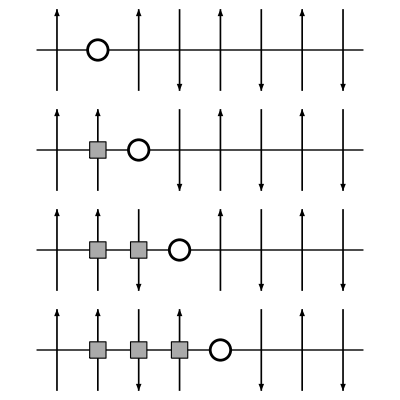

```mathematica
cartoon1=GraphicsGrid[{{g1},{g2},{g5},{g6}},AspectRatio->0.75,Spacings->0]
```

```mathematica
Export["plots/cartoons/cartoon01.png",cartoon1,ImageResolution->300]

(*it = 0;
Do[(
it++;
Export["plots/cartoons/cartoon_a_"<>ToString[it]<>".png",gi,ImageResolution->300]
),{gi, {g1,g2,g3}}]*)
```

plots/cartoons/cartoon01.png

-Graphics-

-Graphics-

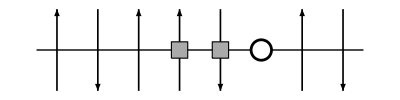

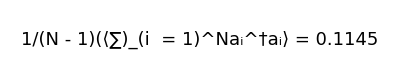

```mathematica
g1=Graphics[(
arrows1=Table[a[n,-h*(-1)^n],{n,1,1}];
arrows2=Table[a[n,-h*(-1)^n],{n,3,8}];
(*arrows3=Table[a[n,h*(-1)^n],{n,8,10}];*)
hole=Table[d[n,0,r,holeFillingColor],{n,{2}}];
sites=Table[d[n,0,0.05,Black],{n,1,8}];
baseline={Line[{{0.5,0},{8.5,0}}]};
(*eraser={e[7,0,1,1]};*)
(*dots=Table[d[6.5+n/4,0,0.025,Black],{n,1,3}];*)
insets={
fontSize=24;
Inset[Style["i",fontSize,Black,FontFamily->"Bookman Old Style"],{4,-1.6}],
Inset[Style["i + n",fontSize,Black,FontFamily->"Bookman Old Style"],{8,-1.6}]
};
Join[baseline,(*sites,*)arrows1,arrows2,(*arrows3,*)hole(*,eraser,dots,insets*)]
)]
g3=Graphics[(
arrows1=Table[a[n,-h*(-1)^n],{n,1,1}];
arrows2=Table[a[n,h*(-1)^n],{n,2,5}];
arrows3=Table[a[n,-h*(-1)^n],{n,7,8}];
magnons=Table[rc[n,0,r,magnonFillingColor],{n,2,5}];
hole=Table[d[n,0,r,holeFillingColor],{n,{6}}];
sites=Table[d[n,0,0.05,Black],{n,1,8}];
baseline={Line[{{0.5,0},{8.5,0}}]};
(*eraser={e[6,0,1,2.25]};
dots=Table[d[5.5+n/4,0,0.025,Black],{n,1,3}];
insets={
fontSize=24;
Inset[Style["i",fontSize,Black,FontFamily->"Bookman Old Style"],{4,-1.6}],
Inset[Style["i + n",fontSize,Black,FontFamily->"Bookman Old Style"],{8,-1.6}]
};*)
Join[baseline,(*sites,*)arrows1,arrows2,arrows3,magnons,hole(*,eraser,dots,insets*)]
)]
g3=Graphics[(
arrows1=Table[a[n,-h*(-1)^n],{n,1,3}];
arrows2=Table[a[n,h*(-1)^n],{n,4,5}];
arrows3=Table[a[n,-h*(-1)^n],{n,7,8}];
magnons=Table[rc[n,0,r,magnonFillingColor],{n,4,5}];
hole=Table[d[n,0,r,holeFillingColor],{n,{6}}];
sites=Table[d[n,0,0.05,Black],{n,1,8}];
baseline={Line[{{0.5,0},{8.5,0}}]};
(*eraser={e[6,0,1,2.25]};
dots=Table[d[5.5+n/4,0,0.025,Black],{n,1,3}];
insets={
fontSize=24;
Inset[Style["i",fontSize,Black,FontFamily->"Bookman Old Style"],{4,-1.6}],
Inset[Style["i + n",fontSize,Black,FontFamily->"Bookman Old Style"],{8,-1.6}]
};*)
Join[baseline,(*sites,*)arrows1,arrows2,arrows3,magnons,hole(*,eraser,dots,insets*)]
)]
g4=Graphics[(
eraser=Table[e[n,0,1,2],{n,1,10}];
hole={d[2.5,2,r,holeFillingColor]};
magnon={d[6,2,r,magnonFillingColor]};
inset={
(*Inset[Style[" hole",24,Black,FontFamily->"Bookman Old Style"],{3.5,1.5}],
Inset[Style[" magnon",24,Black,FontFamily->"Bookman Old Style"],{7.5,1.5}],*)
Inset[Style["1/(N - 1)(⟨∑)_(i  = 1)^Na_i^†a_i⟩ = 0.1145",18,Black,FontFamily->"Bookman Old Style"],{5.5,0}]
};
Join[eraser,(*,hole,magnon,*)inset]
)]
```

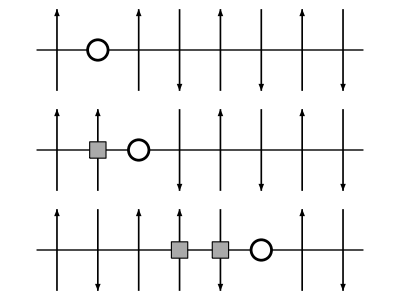

```mathematica
cartoon0=GraphicsGrid[{{g1},{g2},{g3}},AspectRatio->0.75,Spacings->0]
```

```mathematica
Export["plots/cartoons/cartoon0.png",cartoon0,ImageResolution->300]

(*it = 0;
Do[(
it++;
Export["plots/cartoons/cartoon_b_"<>ToString[it]<>".png",gi,ImageResolution->300]
),{gi, {g1,g2,g3}}]*)
```

plots/cartoons/cartoon0.png